CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Thu 1 Jan 2026. Please

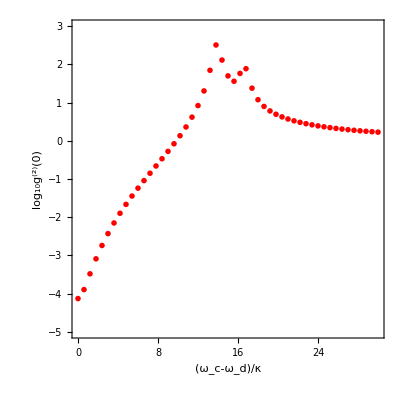

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=4;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=30*κ;
min1=0;      (*max and min value of Δ*)
segment1=50;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=Sqrt[E1^2/(2 E1^2+4 Δ^2+κ^2)];

g=0.01*ωr;


equs=Table[{g*C2*Sqrt[2]+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*Sqrt[6]+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*Sqrt[2]*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*Sqrt[2]+E1/2*C3*Sqrt[3]-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*Sqrt[6]*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*Sqrt[3]-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/(E1^2/(2 E1^2+4 Δ^2+κ^2))^2];


{Δ/κ,logg20},{m,1,50+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Red},PlotMarkers->"OpenMarkers",Frame->True,PlotRange->{{0,30},{-5,3}},AspectRatio->1]
```

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Thu 1 Jan 2026. Please

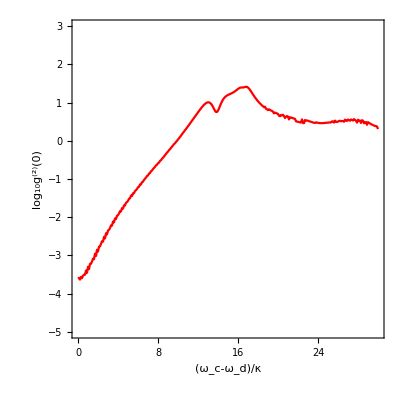

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=16;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=12;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,Sqrt[2],0,0,0},{0,0,0,Sqrt[3],0,0},{0,0,0,0,2,0},{0,0,0,0,0,Sqrt[5]},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,Sqrt[2],0,0,0,0},{0,0,Sqrt[3],0,0,0},{0,0,0,2,0,0},{0,0,0,0,Sqrt[5],0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f;
Jrf=σr1f+σr2f+σr3f+σr4f;
Jxf=Jlf+Jrf;



(*设定参数*)
ωr=4*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;

γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=700;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωr*adaigef.af+g*(adaigef.adaigef.(σl1f)+af.af.(σr1f))+g*(adaigef.adaigef.(σl2f)+af.af.(σr2f))+g*(adaigef.adaigef.(σl3f)+af.af.(σr3f))+g*(adaigef.adaigef.(σl4f)+af.af.(σr4f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=KroneckerProduct[({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-10,t0,1}]];
{m,logg20},{m,0,30,0.1}];



ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->True,PlotStyle->{Red},Frame->True,PlotRange->{{0,30},{-5,3}},AspectRatio->1]
```

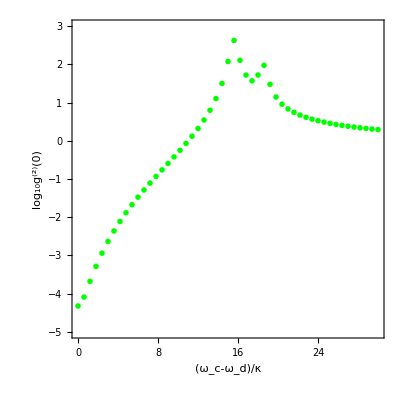

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=5;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=30*κ;
min1=0;      (*max and min value of Δ*)
segment1=50;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=Sqrt[E1^2/(2 E1^2+4 Δ^2+κ^2)];

g=0.01*ωr;


equs=Table[{g*C2*Sqrt[2]+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*Sqrt[6]+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*Sqrt[2]*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*Sqrt[2]+E1/2*C3*Sqrt[3]-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*Sqrt[6]*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*Sqrt[3]-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/(E1^2/(2 E1^2+4 Δ^2+κ^2))^2];


{Δ/κ,logg20},{m,1,50+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Green},PlotMarkers->"OpenMarkers",Frame->True,PlotRange->{{0,30},{-5,3}},AspectRatio->1]
```

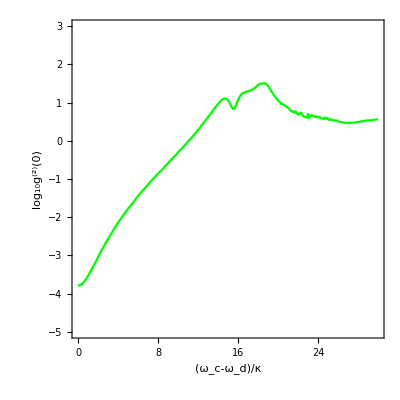

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=32;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=14;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,Sqrt[2],0,0,0},{0,0,0,Sqrt[3],0,0},{0,0,0,0,2,0},{0,0,0,0,0,Sqrt[5]},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,Sqrt[2],0,0,0,0},{0,0,Sqrt[3],0,0,0},{0,0,0,2,0,0},{0,0,0,0,Sqrt[5],0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx,unity2];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz,unity2];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr,unity2];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl,unity2];
σx5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σx];
σz5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σz];
σr5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σr];
σl5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f+σl5f;
Jrf=σr1f+σr2f+σr3f+σr4f+σr5f;
Jxf=Jlf+Jrf;



(*设定参数*)
ωr=4*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;

γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=700;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωq/2*σz5f+ωr*adaigef.af+g*(adaigef.adaigef.(σl1f)+af.af.(σr1f))+g*(adaigef.adaigef.(σl2f)+af.af.(σr2f))+g*(adaigef.adaigef.(σl3f)+af.af.(σr3f))+g*(adaigef.adaigef.(σl4f)+af.af.(σr4f))+g*(adaigef.adaigef.(σl5f)+af.af.(σr5f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl5fcut=Take[SToH.σl5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr5fcut=Take[SToH.σr5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=KroneckerProduct[({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr5fcut,σl5fcut,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,g,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf)+γ/2*(2*σl5fcut.ρf.σr5fcut-ρf.σr5fcut.σl5fcut-σr5fcut.σl5fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-10,t0,0.1}]];
{m,logg20},{m,0,30,0.1}];



ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->True,PlotStyle->{Green},Frame->True,PlotRange->{{0,30},{-5,3}},AspectRatio->1]
```

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Thu 1 Jan 2026. Please

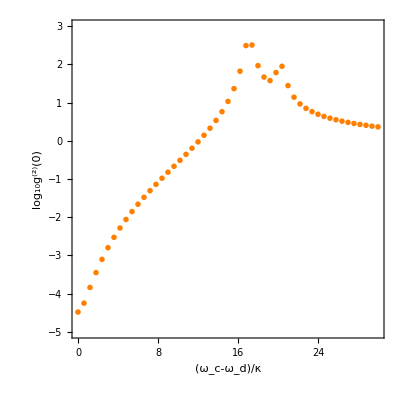

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=6;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=30*κ;
min1=0;      (*max and min value of Δ*)
segment1=50;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=Sqrt[E1^2/(2 E1^2+4 Δ^2+κ^2)];

g=0.01*ωr;


equs=Table[{g*C2*Sqrt[2]+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*Sqrt[6]+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*Sqrt[2]*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*Sqrt[2]+E1/2*C3*Sqrt[3]-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*Sqrt[6]*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*Sqrt[3]-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/(E1^2/(2 E1^2+4 Δ^2+κ^2))^2];


{Δ/κ,logg20},{m,1,50+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Orange},PlotMarkers->"OpenMarkers",Frame->True,PlotRange->{{0,30},{-5,3}},AspectRatio->1]
```

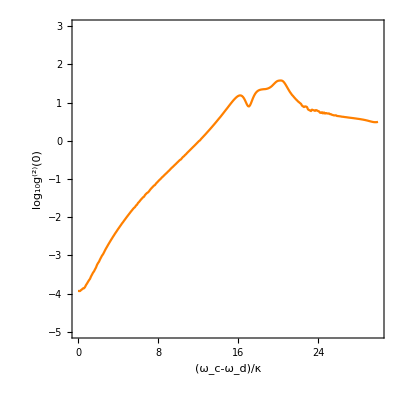

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=64;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=16;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,Sqrt[2],0,0,0},{0,0,0,Sqrt[3],0,0},{0,0,0,0,2,0},{0,0,0,0,0,Sqrt[5]},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,Sqrt[2],0,0,0,0},{0,0,Sqrt[3],0,0,0},{0,0,0,2,0,0},{0,0,0,0,Sqrt[5],0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2,unity2,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2,unity2,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2,unity2,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2,unity2,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx,unity2,unity2];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz,unity2,unity2];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr,unity2,unity2];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl,unity2,unity2];
σx5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σx,unity2];
σz5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σz,unity2];
σr5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σr,unity2];
σl5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σl,unity2];
σx6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σx];
σz6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σz];
σr6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σr];
σl6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f+σl5f+σl6f;
Jrf=σr1f+σr2f+σr3f+σr4f+σr5f+σr6f;
Jxf=Jlf+Jrf;



(*设定参数*)
ωr=4*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;

γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=700;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωq/2*σz5f+ωq/2*σz6f+ωr*adaigef.af+g*(adaigef.adaigef.(σl1f)+af.af.(σr1f))+g*(adaigef.adaigef.(σl2f)+af.af.(σr2f))+g*(adaigef.adaigef.(σl3f)+af.af.(σr3f))+g*(adaigef.adaigef.(σl4f)+af.af.(σr4f))+g*(adaigef.adaigef.(σl5f)+af.af.(σr5f))+g*(adaigef.adaigef.(σl6f)+af.af.(σr6f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl5fcut=Take[SToH.σl5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr5fcut=Take[SToH.σr5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl6fcut=Take[SToH.σl6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr6fcut=Take[SToH.σr6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=KroneckerProduct[({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr6fcut,σl6fcut,σr5fcut,σl5fcut,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,g,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf)+γ/2*(2*σl5fcut.ρf.σr5fcut-ρf.σr5fcut.σl5fcut-σr5fcut.σl5fcut.ρf)+γ/2*(2*σl6fcut.ρf.σr6fcut-ρf.σr6fcut.σl6fcut-σr6fcut.σl6fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-10,t0,0.1}]];
{m,logg20},{m,0,30,0.1}];



ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->True,PlotStyle->{Orange},Frame->True,PlotRange->{{0,30},{-5,3}},AspectRatio->1]
```

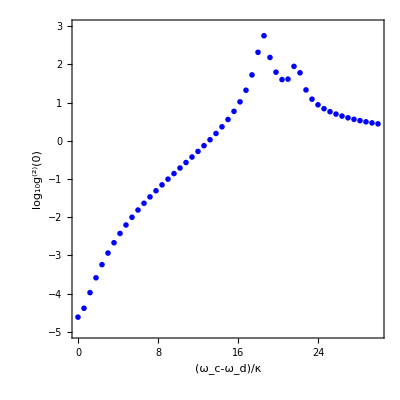

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=7;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=30*κ;
min1=0;      (*max and min value of Δ*)
segment1=50;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=Sqrt[E1^2/(2 E1^2+4 Δ^2+κ^2)];

g=0.01*ωr;


equs=Table[{g*C2*Sqrt[2]+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*Sqrt[6]+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*Sqrt[2]*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*Sqrt[2]+E1/2*C3*Sqrt[3]-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*Sqrt[6]*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*Sqrt[3]-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/(E1^2/(2 E1^2+4 Δ^2+κ^2))^2];


{Δ/κ,logg20},{m,1,50+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Blue},PlotMarkers->"OpenMarkers",Frame->True,PlotRange->{{0,30},{-5,3}},AspectRatio->1]
```

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Thu 1 Jan 2026. Please

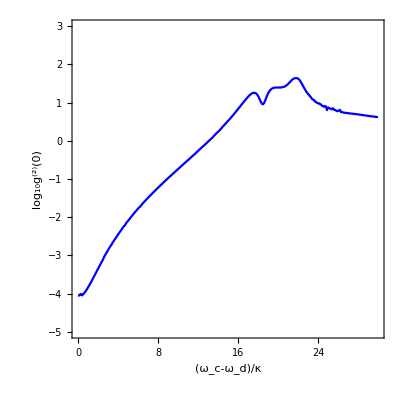

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=128;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=18;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,Sqrt[2],0,0,0},{0,0,0,Sqrt[3],0,0},{0,0,0,0,2,0},{0,0,0,0,0,Sqrt[5]},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,Sqrt[2],0,0,0,0},{0,0,Sqrt[3],0,0,0},{0,0,0,2,0,0},{0,0,0,0,Sqrt[5],0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2,unity2,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2,unity2,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2,unity2,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2,unity2,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2,unity2,unity2,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2,unity2,unity2,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2,unity2,unity2,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2,unity2,unity2,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx,unity2,unity2,unity2];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz,unity2,unity2,unity2];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr,unity2,unity2,unity2];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl,unity2,unity2,unity2];
σx5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σx,unity2,unity2];
σz5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σz,unity2,unity2];
σr5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σr,unity2,unity2];
σl5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σl,unity2,unity2];
σx6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σx,unity2];
σz6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σz,unity2];
σr6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σr,unity2];
σl6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σl,unity2];
σx7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σx];
σz7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σz];
σr7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σr];
σl7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f+σl5f+σl6f+σl7f;
Jrf=σr1f+σr2f+σr3f+σr4f+σr5f+σr6f+σr7f;
Jxf=Jlf+Jrf;



(*设定参数*)
ωr=4*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;

γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=700;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωq/2*σz5f+ωq/2*σz6f+ωq/2*σz7f+ωr*adaigef.af+g*(adaigef.adaigef.(σl1f)+af.af.(σr1f))+g*(adaigef.adaigef.(σl2f)+af.af.(σr2f))+g*(adaigef.adaigef.(σl3f)+af.af.(σr3f))+g*(adaigef.adaigef.(σl4f)+af.af.(σr4f))+g*(adaigef.adaigef.(σl5f)+af.af.(σr5f))+g*(adaigef.adaigef.(σl6f)+af.af.(σr6f))+g*(adaigef.adaigef.(σl7f)+af.af.(σr7f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl5fcut=Take[SToH.σl5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr5fcut=Take[SToH.σr5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl6fcut=Take[SToH.σl6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr6fcut=Take[SToH.σr6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl7fcut=Take[SToH.σl7f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr7fcut=Take[SToH.σr7f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=KroneckerProduct[({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr7fcut,σl7fcut,σr6fcut,σl6fcut,σr5fcut,σl5fcut,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,g,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf)+γ/2*(2*σl5fcut.ρf.σr5fcut-ρf.σr5fcut.σl5fcut-σr5fcut.σl5fcut.ρf)+γ/2*(2*σl6fcut.ρf.σr6fcut-ρf.σr6fcut.σl6fcut-σr6fcut.σl6fcut.ρf)+γ/2*(2*σl7fcut.ρf.σr7fcut-ρf.σr7fcut.σl7fcut-σr7fcut.σl7fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-10,t0,0.1}]];
{m,logg20},{m,0,30,0.1}];



ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->True,PlotStyle->{Blue},Frame->True,PlotRange->{{0,30},{-5,3}},AspectRatio->1]
```

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,BaseStyle->{FontSize->16,FontFamily->"Calibri"}]
```